Run the following line to add the package to the path (unless this has already been done)

```mathematica
AppendTo[$Path,NotebookDirectory[]];
```

Now we can load the package

```mathematica
<<RiemannHilbert`;
```

## Cauchy and Hilbert Transforms

### Over the unit interval

We can define a function over an interval as

```mathematica
f=Fun[Exp[I #]&,Line[{-1,1}]];
```

We can evaluate at point:

```mathematica
f[.5]
```

0.877583+0.479426 ⅈ

```mathematica
Exp[I .5]
```

0.877583+0.479426 ⅈ

The output format is its real (in blue) and imaginary (in red) parts

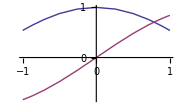

```mathematica
f
```

The Cauchy transform at a point in the complex plane can be evaluated via

```mathematica
Cauchy[f,1. ⅈ+2.]
```

0.0502639+0.125313 ⅈ

Using NIntegrate we obtain the same result

```mathematica
1/(2π ⅈ)NIntegrate[Exp[ⅈ x]/(x-(1.ⅈ+2.)),{x,-1,1}]
```

0.0502639+0.125313 ⅈ

Near the domain of f, the Cauchy transform has a jump

```mathematica
{Cauchy[f,0.1+0.0000001 ⅈ],Cauchy[f,0.1-0.0000001 ⅈ]}
```

{0.79494+0.0971639 ⅈ,-0.200064-0.00266951 ⅈ}

We can reliably evaluate the left and right limits via

```mathematica
{Cauchy[+1,f,0.1],Cauchy[-1,f,0.1]}
```

{0.79494+0.0971639 ⅈ,-0.200064-0.00266952 ⅈ}

From Plemelj’s lemma, taking the difference we get back f

```mathematica
Cauchy[+1,f,0.1]-Cauchy[-1,f,0.1]-f[0.1]
```

1.11022×10^-16+6.93889×10^-17 ⅈ

Taking the sum we get the Hilbert transform

```mathematica
ⅈ(Cauchy[+1,f,0.1]+Cauchy[-1,f,0.1])
```

-0.0944944+0.594875 ⅈ

This is the definition of

```mathematica
Hilbert[f,0.1]
```

-0.0944944+0.594875 ⅈ

This is equal to the NIntegrate computed version:

```mathematica
1/π NIntegrate[Exp[ⅈ x]/(x-0.1),{x,-1,0.1,1},PrincipalValue->True]
```

-0.0944944+0.594875 ⅈ

### Over the real line of a function with the same asymptotic series at ±∞

We can define a function over the real line (a mapped Laurent series) as

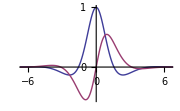

```mathematica
f=LFun[If[InfinityQ[#],0,Exp[ⅈ #] Sech[#]]&,Line[{-∞,∞}]]
```

Like an interval, we can evaluate the Cauchy transform in the complex plane (note that NIntegrate needs high precision arithmetic to compute the same value)

```mathematica
Cauchy[f,2. ⅈ]-1/(2 π ⅈ)NIntegrate[(Exp[ⅈ t] Sech[t])/(t-2 ⅈ),{t,-∞,∞},WorkingPrecision->30]
```

7.77989×10^-14+0. ⅈ

We can also do the ±1 values, and in fact we can compute it globally

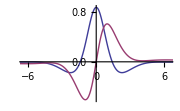
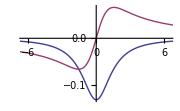

```mathematica
{Cauchy[+1,f],Cauchy[-1,f]}
```

And here's the Hilbert transform

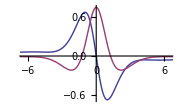

```mathematica
Hilbert[f]
```

Alternatively, we can use two half lines

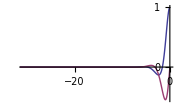
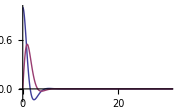

```mathematica
hf={ZeroAtInfinityFun[Exp[ⅈ #] Sech[#]&,Line[{-∞,0}]],ZeroAtInfinityFun[Exp[ⅈ #] Sech[#]&,Line[{0,∞}]]}
```

This also computes the Cauchy transform (with a couple extra digits of accuracy)

```mathematica
Cauchy[hf,2. ⅈ]-1/(2 π ⅈ)NIntegrate[(Exp[ⅈ t] Sech[t])/(t-2 ⅈ),{t,-∞,∞},WorkingPrecision->30]
```

-4.96825×10^-15+2.498×10^-16 ⅈ

Since the solution is bounded (unlike the interval case), we can also compute the ±1 limits globally

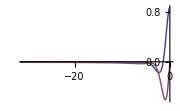
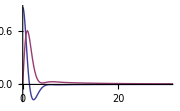
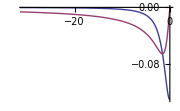
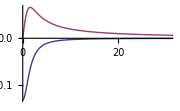

```mathematica
{Cauchy[+1,hf],Cauchy[-1,hf]}
```

And the Hilbert transform matches

```mathematica
Hilbert[hf,0.1]-Hilbert[f,0.1]
```

-9.44245×10^-14-1.85851×10^-13 ⅈ

At a single point they are both O(n log n) operations, hence comparable

```mathematica
{Hilbert[hf,0.1]//Timing//First,Hilbert[f,0.1]//Timing//First}
```

{0.121247,0.079614}

Globally, two half lines is an O(n^2) operation while one real line is O(n log n)

```mathematica
{Hilbert[hf]//Timing//First,Hilbert[f]//Timing//First}
```

{4.97266,0.109514}

### Over the real line of a function with different asymptotic series at ±∞

The Laurent based approach is not as accurate for a function which is not smooth when mapped to the unit circle (we fix it at 500 points since adaptivity won't converge)

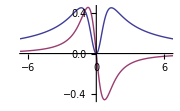

```mathematica
f=LFun[If[InfinityQ[#],0,Erf[#]/(#+ⅈ)]&,Line[{-∞,∞}],500]
```

Now the Cauchy transform is innaccurate:

```mathematica
Cauchy[f,2. ⅈ]-1/(2 π ⅈ)NIntegrate[1/(t-2 ⅈ)Erf[t]/(t+ⅈ),{t,-∞,∞},WorkingPrecision->30]
```

-7.33048×10^-6+0. ⅈ

Two half lines do not have this issue

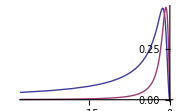
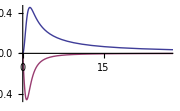

```mathematica
hf={ZeroAtInfinityFun[Erf[#]/(#+ⅈ)&,Line[{-∞,0}]],ZeroAtInfinityFun[Erf[#]/(#+ⅈ)&,Line[{0,∞}]]}
```

The Cauchy transform is still accurate

```mathematica
Cauchy[hf,2. ⅈ]-1/(2 π I)NIntegrate[1/(t-2 ⅈ)Erf[t]/(t+ⅈ),{t,-∞,∞},WorkingPrecision->30]
```

4.85723×10^-16-2.22045×10^-16 ⅈ

## Hastings–McLeod

We now setup the Painlevé II RH problem, for the Hastings–McLeod solution, cf. [Fokas et al. 2006].

### Setting up the jump curves

We want to solve the RH problem

	 Φ^+= Φ^-G ,Φ[∞] = 0

where G depends on x.  Then the solution to Painlevé II is

	 p[x]=2 lim_(z→∞) z Φ[z]⟦1,2⟧

The steps we need to take are

	(a) Define a list of Fun's which represent the jump curve G.
	 (b) Use RHSolver to find a function U defined on the same curve as G. This U satisfies  Φ[z] = IdentityMatrix[2] + Cauchy[U,z].
	(c) Compute p, using lim_(z→∞) z Φ[z]⟦1,2⟧, which can be found by integrating U.

To setup G, we first choose the Stokes' multipliers

```mathematica
s//Clear;
{s[1],s[2],s[3]}={I,0,-I};
{s[4],s[5],s[6]}=-Array[s,3];
```

We define functions for the jump function

```mathematica
θ[x_,z_]:=(8 I)/3 z^3+ 2 I x z;
G//Clear;
G[_][_,_?InfinityQ]:=({{1, 0}, {0, 1}});
G[1][x_,z_]:=({{1, 0}, {s[1]Exp[θ[x,z]], 1}})/.Underflow[]->0;
G[3][x_,z_]:=({{1, 0}, {s[3]Exp[θ[x,z]], 1}})/.Underflow[]->0;
G[4][x_,z_]:=({{1, s[4]Exp[-θ[x,z]]}, {0, 1}})/.Underflow[]->0;
G[6][x_,z_]:=({{1, s[6]Exp[-θ[x,z]]}, {0, 1}})/.Underflow[]->0;
Off[General::"unfl"];
```

We need to construct Funs (interpolations by mapped Chebyshev polynomials) of the jump functions defined above.  GG returns the jump curve sampled at n points along each ray.

```mathematica
GG[n_,x_]:={
Fun[G[1][x,#]&,Line[{0,∞ Exp[I π/6]}],n],
Fun[G[3][x,#]&,Line[{0,∞ Exp[I (π/6+2 π/3)]}],n],
Fun[G[4][x,#]&,Line[{0,∞ Exp[I (-π/6-2 π/3)]}],n],
Fun[G[6][x,#]&,Line[{0,∞ Exp[I (-π/6)]}],n]
};
```

We can plot the domain of our jump curve

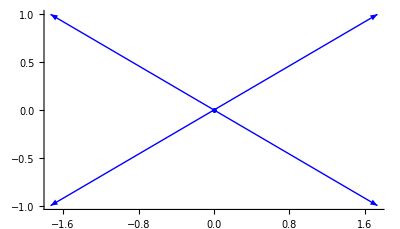

```mathematica
GG[80,0.]//DomainPlot
```

### The solution to the RH problem at x = 0

We can compute the solution to a RH problem with the jump curve GG using the command

```mathematica
U//Clear;
n=50;
U=RHSolve[GG[n,0.]];
```

The solution is the identity matrix + the Cauchy transform of U.  Here we demonstrate its accuracy, by comparing the + and - values with the jump curve at a point along the first ray:

```mathematica
IdentityMatrix[2]+Cauchy[U,.5Exp[I π/6]+10.^(-11) I]-(IdentityMatrix[2]+Cauchy[U,.5Exp[I π/6]-10.^(-11) I]).G[1][0.,0.5Exp[I π/6]]
```

{{-1.19909×10^-8-8.798×10^-9 ⅈ,3.83597×10^-12-3.03182×10^-12 ⅈ},{-1.41104×10^-9+2.08668×10^-8 ⅈ,-5.18252×10^-13-5.95819×10^-13 ⅈ}}

What we actually want is the limit of the Cauchy transform 

	2lim_(z→∞) z 1/(2π ⅈ)∫_Domain[U] (U[t]⟦1,2⟧)/(t-z)ⅆt  = -1/(π ⅈ)∫_Domain[U] U[t]⟦1,2⟧ⅆt 
	
Thus we obtain the following approximation

```mathematica
-1/(π ⅈ)DomainIntegrate[U]⟦1,2⟧
```

-0.367062+0. ⅈ

The PainleveII routine matches this value

```mathematica
PainleveII[{s[1],s[2],s[3]},0.]
```

-0.367062+0. ⅈ

In the next section, we will compare this value (and those for other values of x) to precomputed values available from [Prähofer & Spohn 2003]

### Using RHSolver to speed up computation at multiple values of x

RHSolve, used in the previous section, recomputes the same matrices of Cauchy transform values for each value of x. RHSolver precomputes these matrices (for a given n), significantly speeding up evaluation for multiple x's.

```mathematica
R//Clear;n//Clear;x//Clear;
R[n_]:=R[n]=RHSolver[GG[n,0.]];
```

U returns the jump curve, so that the top row of the solution to the RH problem is IdentityMatrix[2] + Cauchy[U[n,x], z]

```mathematica
U//Clear;
U[n_,x_]:=U[n,x]=R[n][GG[n,x]];
```

p is the value of the Hastings–McLeod solution

```mathematica
p//Clear;
p[n_,x_]:=p[n,x]=-1/(π ⅈ) DomainIntegrate[U[n,x]]⟦1,2⟧
```

We can now evaluate the Hastings-McLeod at points (real or complex)

```mathematica
{p[50,0.],p[50,1. I],p[50,1.]}
```

{-0.367062+0. ⅈ,-0.311544+0.319503 ⅈ,-0.135644-3.53395×10^-17 ⅈ}

We can plot the solution (this takes half a second per point, so almost a minute to generate the plot)

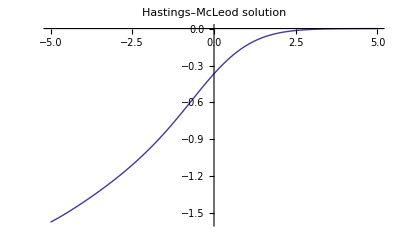

```mathematica
Monitor[TablePlot[p[50,x],{x,-5.,5.,.1},PlotLabel->"Hastings–McLeod solution"],x]
```

We can compare with the [Prähofer & Spohn 2003] computed values:

```mathematica
data=Partition[ReadList["RiemannHilbert/Data/McLeodSolution.txt",Number],7];
data2=Select[data,-3.<=First[#]≤3.&];
```

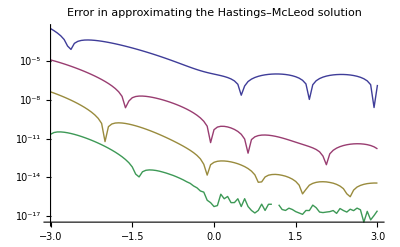

```mathematica
Monitor[Block[{x},
ListLineLogPlot[{
({x=#⟦1⟧,p[25,#⟦1⟧]-#⟦3⟧//Abs})&/@data2,
{x=#⟦1⟧,p[50,#⟦1⟧]-#⟦3⟧//Abs}&/@data2,
({x=#⟦1⟧,p[75,#⟦1⟧]-#⟦3⟧//Abs})&/@data2,
({x=#⟦1⟧,p[100,#⟦1⟧]-#⟦3⟧//Abs})&/@data2
},PlotLabel->"Error in approximating the Hastings–McLeod solution"]
],x]
```

We can even do a complex plot: (which takes some time)

```mathematica
Monitor[
TablePlot3D[Abs[p[50,x+I y]],{x,-3.,3.,0.25},{y,-3.5,3.5,0.25},PlotLabel->"Hastings–McLeod solution in the complex plane"]
,{x,y}]
```

-Graphics3D-

### Computing the derivative of the Hastings–McLeod solution

We can also compute the derivative of the Hastings–McLeod solution.  We need to use a different right hand side to the RH problem, since the derivative satisfies 

	Φ_x^+ – Φ_x^- G =  Φ^- G_x, Φ_x(∞) = 0,
	
by differentiation of both sides.  First we construct the derivative with respect to x of the jump matrix GG.

```mathematica
θx[x_,z_]:= 2 I  z;
Gx//Clear;
Gx[_][_,_?InfinityQ]:=({{0, 0}, {0, 0}});
Gx[1][x_,z_]:=({{0, 0}, {s[1]θx[x,z] Exp[θ[x,z]], 0}})/.Underflow[]->0;
Gx[3][x_,z_]:=({{0, 0}, {s[3]θx[x,z] Exp[θ[x,z]], 0}})/.Underflow[]->0;
Gx[4][x_,z_]:=({{0, -θx[x,z] s[4]Exp[-θ[x,z]]}, {0, 0}})/.Underflow[]->0;
Gx[6][x_,z_]:=({{0, -θx[x,z] s[6]Exp[-θ[x,z]]}, {0, 0}})/.Underflow[]->0;
GGx[n_,x_]:={Fun[Gx[1][x,#]&,Line[{0,∞ Exp[I π/6]}],n],Fun[Gx[3][x,#]&,Line[{0,∞ Exp[I (π/6+2 π/3)]}],n],
Fun[Gx[4][x,#]&,Line[{0,∞ Exp[I (-π/6-2 π/3)]}],n],
Fun[Gx[6][x,#]&,Line[{0,∞ Exp[I (-π/6)]}],n]
};
```

We need Φ^-, which is the identity matrix plus the cauchy transform of U.  The function CauchyOperator precomputes the Cauchy matrices for a fixed n.  The function AddIdentityMatrix adds the identity matrix to a list of Funs.

Alternatively, we could have written

	Φm[n_, x_] := Φm[n, x] =  Cauchy[-1,U[n, x]]//AddIdentityMatrix;

```mathematica
Φm//Clear;
Cm//Clear;
Cm[n_]:=Cm[n]=CauchyOperator[-1,R[n]];
Φm[n_,x_]:=Φm[n,x]=Cm[n][U[n,x]]//AddIdentityMatrix;
```

We now use our precomputed RHSolver.  Specifying a second argument is equivalent to changing the right–hand side.  We want the new right-hand side to be  Φ^- G_x.  The multiplication is accomplished using FunListDot, which takes two lists of Funs and dots the lists component-wise

```mathematica
Ux//Clear;
Ux[n_,x_]:=Ux[n,x]=R[n][GG[n,x],Φm[n,x]~FunListDot~GGx[n,x]]
```

We can now define the derivative of the solution

```mathematica
px//Clear;
px[n_,x_]:=px[n,x]=-1/(π ⅈ) DomainIntegrate[Ux[n,x]]⟦1,2⟧
```

This gives a value at x = 0

```mathematica
px[75,0.]
```

0.295372+0. ⅈ

```mathematica
PainleveIID[{s[1],s[2],s[3]},0.]
```

0.295372+0. ⅈ

We can plot the derivative of the solution (chopping off the small imaginary part that is due to round-off error)

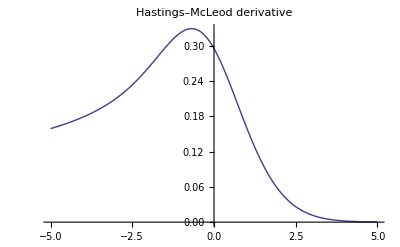

```mathematica
Monitor[TablePlot[px[75,x]//Re,{x,-5.,5.,.1},PlotLabel->"Hastings–McLeod derivative"],x]
```

We can compare this too with the values from [Prähofer & Spohn 2003]

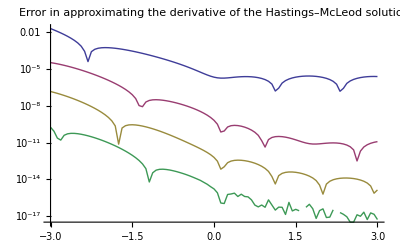

```mathematica
ListLineLogPlot[{
({#⟦1⟧,px[25,#⟦1⟧]-#⟦4⟧//Abs})&/@data2,
({#⟦1⟧,px[50,#⟦1⟧]-#⟦4⟧//Abs})&/@data2,
({#⟦1⟧,px[75,#⟦1⟧]-#⟦4⟧//Abs})&/@data2,
({#⟦1⟧,px[100,#⟦1⟧]-#⟦4⟧//Abs})&/@data2
},PlotLabel->"Error in approximating the derivative of the Hastings–McLeod solution"]
```

## Homogeneous Painlevé II equation

To speed up the algorithm, in the Hastings–McLeod solution we only used 4 of the 6 rays.  There is no problem with adapting it to the full six rays, as the following example demonstrates:

```mathematica
s//Clear;
{s[1],s[2],s[3]}={1,2,1/3.};
{s[4],s[5],s[6]}=-Array[s,3];
```

```mathematica
θ[x_,z_]:=(8 I)/3 z^3+ 2 I x z;
G//Clear;
G[_][_,_?InfinityQ]:=({{1, 0}, {0, 1}});
G[1][x_,z_]:=({{1, 0}, {s[1]Exp[θ[x,z]], 1}})/.Underflow[]->0;
G[2][x_,z_]:=({{1, s[2]Exp[-θ[x,z]]}, {0, 1}})/.Underflow[]->0;
G[3][x_,z_]:=({{1, 0}, {s[3]Exp[θ[x,z]], 1}})/.Underflow[]->0;
G[4][x_,z_]:=({{1, s[4]Exp[-θ[x,z]]}, {0, 1}})/.Underflow[]->0;
G[5][x_,z_]:=({{1, 0}, {s[5]Exp[θ[x,z]], 1}})/.Underflow[]->0;
G[6][x_,z_]:=({{1, s[6]Exp[-θ[x,z]]}, {0, 1}})/.Underflow[]->0;
GG[n_,x_]:={
Fun[G[1][x,#]&,Line[{0,∞ Exp[I π/6]}],n],
Fun[G[2][x,#]&,Line[{0,∞ Exp[I (π/6+π/3)]}],n],
Fun[G[3][x,#]&,Line[{0,∞ Exp[I (π/6+2 π/3)]}],n],
Fun[G[4][x,#]&,Line[{0,∞ Exp[I (-π/6-2 π/3)]}],n],
Fun[G[5][x,#]&,Line[{0,∞ Exp[I (-π/6-π/3)]}],n],
Fun[G[6][x,#]&,Line[{0,∞ Exp[I (-π/6)]}],n]
};
```

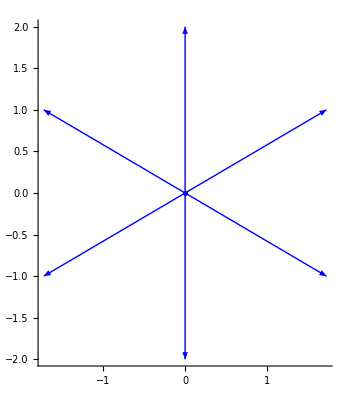

```mathematica
GG[50,0.]//DomainPlot
```

Since we don't need derivatives, we only need the top row of the RH problem (which takes less time to compute).  This is accomplished using the RHSolverTop command.

```mathematica
Clear[R,n,x,U,p];
R[n_]:=R[n]=RHSolverTop[GG[n,0.]];
U[n_,x_]:=U[n,x]=R[n][GG[n,x]];
p[n_,x_]:=p[n,x]=-1/(π ⅈ) DomainIntegrate[U[n,x]]⟦2⟧
```

We can evaluate at x = 0

```mathematica
p[50,0.]
```

-0.500684+0.117485 ⅈ

```mathematica
PainleveII[{s[1],s[2],s[3]},0.]
```

-0.500684+0.117485 ⅈ

Here's the solution (real part in blue and imaginary part in red) for the new choice of Stokes' multipliers

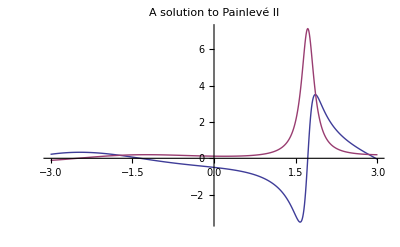

```mathematica
Monitor[ReImTablePlot[p[25,x],{x,-3.,3.,.01},PlotRange->All,PlotLabel->"A solution to Painlevé II"],x]
```

## Painleve III

The Painlevé III differential equation is

	u'' = (u')^2/u-u'/x+4/x(Θ_0 u^2+1-Θ_∞) + 4 u^3-4/u

The following example is based on an example in [Olver 2010] constructed from the RH problem in [Fokas et al. 2006].

### Setting up the jump curves

We choose an arbitrary choice of Stokes' multipliers, and the constants Θ_∞ and Θ_0.  (In case it seems odd that we have 3 degrees of freedom where the ODE with initial conditions only has 2 degrees of freedom, note that there is an equivalency class for the Stokes' multipliers.)

```mathematica
Θ∞=1+123/1000;
Θ0=3+43/100;
s//Clear;
s[1,0]=1;
s[2,0]=2;
s[2,∞]=3;
s[1,∞]=s[1,∞]/.Solve[2 Cos[π Θ0]+s[1,0]s[2,0]Exp[-I π Θ0]==2 Cos[π Θ∞]+s[1,∞]s[2,∞]Exp[I π Θ∞],s[1,∞]]//First;
```

We require a matrix EE, which is similar to an eigenvalue matrix.  We determine this matrix by solving a system of equations, where we impose that the bottom row of EE is (1,1) (which may break down for other choices of Stokes multipliers and Θ constants).

```mathematica
EE//Clear;
EE=({{e1, e2}, {1, 1}})/.First[Solve[Thread[Flatten[
({{e1, e2}, {1, 1}}).({{1+s[1,∞] s[2,∞], s[1,∞]}, {s[2,∞], 1}}).({{Exp[ I π Θ∞], 0}, {0, Exp[- I π Θ∞]}})-({{1+s[1,0] s[2,0], s[1,0]}, {s[2,0], 1}}).({{Exp[- I π Θ0], 0}, {0, Exp[ I π Θ0]}}).({{e1, e2}, {1, 1}})
]=={0,0,0,0}],{e1,e2}]]//N;
```

We can now construct the jump curve functions

```mathematica
G//Clear;
x//Clear;
z//Clear;
θ//Clear;
θ[x_,z_]:=(I x)/2(z-1/z) ;
G[_,_][_,_?InfinityQ]:=IdentityMatrix[2];
G[_,_][_,_?ZeroQ]:=IdentityMatrix[2];
G[3,2][x_,z_]=({{Exp[θ[x,z]] z^(Θ0/2 ), 0}, {0, Exp[-θ[x,z]] z^(-Θ0/2 )}}).EE.({{z^(Θ∞/2 ) Exp[-θ[x,z]], 0}, {0, z^(-Θ∞/2 ) Exp[θ[x,z]]}});
G[∞,3][x_,z_]=({{1, -s[1,∞] z^(-Θ∞ ) Exp[2 θ[x,z]]}, {0, 1}});
G[4,0][x_,z_]=({{1, -s[1,0] z^(Θ0 ) Exp[2 θ[x,z]]}, {0, 1}});
G[1,4][x_,z_]=({{Exp[θ[x,z]] PowerBranch[z,1/2 Θ0,-π/2], -s[1,0]Exp[θ[x,z]] PowerBranch[z,1/2 Θ0,-π/2]}, {0, Exp[-θ[x,z]]PowerBranch[z,-1/2 Θ0,-π/2]}}).EE.({{PowerBranch[z,Θ∞/2 ,-π/2]Exp[-θ[x,z]], s[1,∞]PowerBranch[z,-Θ∞/2 ,-π/2]Exp[θ[x,z]]}, {0, PowerBranch[z,-Θ∞/2 ,-π/2]Exp[θ[x,z]]}});
G[1,2][x_,z_]=({{Exp[θ[x,z]] z^(-Θ∞/2 ), 0}, {0, Exp[-θ[x,z]] z^(Θ∞/2 )}}).Inverse[EE].({{PowerBranch[z,-Θ0/2 ,0]Exp[I π Θ0-θ[x,z]], 0}, {-s[2,0]PowerBranch[z,-Θ0/2 ,0]Exp[-I π Θ0 - θ[x,z]], PowerBranch[z,Θ0/2 ,0]Exp[θ[x,z]-I π Θ0]}});
G[3,4][x_,z_]=({{Exp[θ[x,z]] z^(-Θ∞/2 ), -s[1,∞] Exp[θ[x,z]]  z^(-Θ∞/2 )}, {0, Exp[-θ[x,z]] z^(Θ∞/2 )}}).Inverse[EE].({{z^(-Θ0/2 ) Exp[-θ[x,z]], 0}, {0, z^(Θ0/2 ) Exp[θ[x,z]]}});
G[2,0][x_,z_]=({{1, 0}, {-s[2,0] PowerBranch[z,-Θ0,0] Exp[-2 θ[x,z]], 1}});
G[∞,1][x_,z_]=({{1, 0}, {-s[2,∞] PowerBranch[z,Θ∞,-π/2] Exp[-2 θ[x,z]], 1}});
```

We also need the derivative with respect to x

```mathematica
Gx//Clear;
θx[x_,z_]:=I/2(z-1/z) ;
Gx[_,_][_,_?InfinityQ]:=ZeroMatrix[2];
Gx[_,_][_,_?ZeroQ]:=ZeroMatrix[2];
Gx[3,2][x_,z_]=({{θx[x,z] Exp[θ[x,z]] z^(Θ0/2 ), 0}, {0, -θx[x,z]  Exp[-θ[x,z]] z^(-Θ0/2 )}}).EE.({{z^(Θ∞/2 ) Exp[-θ[x,z]], 0}, {0, z^(-Θ∞/2 ) Exp[θ[x,z]]}})+({{Exp[θ[x,z]] z^(Θ0/2 ), 0}, {0, Exp[-θ[x,z]] z^(-Θ0/2 )}}).EE.({{-z^(Θ∞/2 )θx[x,z]  Exp[-θ[x,z]], 0}, {0, z^(-Θ∞/2 )θx[x,z]   Exp[θ[x,z]]}});
Gx[∞,3][x_,z_]=({{0, -2 θx[x,z]  s[1,∞] z^(-Θ∞ ) Exp[2 θ[x,z]]}, {0, 0}});
Gx[4,0][x_,z_]=({{0, -2 θx[x,z]  s[1,0] z^(Θ0 ) Exp[2 θ[x,z]]}, {0, 0}});
Gx[1,4][x_,z_]=({{θx[x,z] Exp[θ[x,z]] PowerBranch[z,1/2 Θ0,-π/2], -s[1,0]θx[x,z] Exp[θ[x,z]] PowerBranch[z,1/2 Θ0,-π/2]}, {0, -θx[x,z] Exp[-θ[x,z]]PowerBranch[z,-1/2 Θ0,-π/2]}}).EE.({{PowerBranch[z,Θ∞/2 ,-π/2]Exp[-θ[x,z]], s[1,∞]PowerBranch[z,-Θ∞/2 ,-π/2]Exp[θ[x,z]]}, {0, PowerBranch[z,-Θ∞/2 ,-π/2]Exp[θ[x,z]]}})+({{Exp[θ[x,z]] PowerBranch[z,1/2 Θ0,-π/2], -s[1,0]Exp[θ[x,z]] PowerBranch[z,1/2 Θ0,-π/2]}, {0, Exp[-θ[x,z]]PowerBranch[z,-1/2 Θ0,-π/2]}}).EE.({{-θx[x,z] PowerBranch[z,Θ∞/2 ,-π/2]Exp[-θ[x,z]], s[1,∞]θx[x,z] PowerBranch[z,-Θ∞/2 ,-π/2]Exp[θ[x,z]]}, {0, θx[x,z] PowerBranch[z,-Θ∞/2 ,-π/2]Exp[θ[x,z]]}});
Gx[1,2][x_,z_]=({{Exp[θ[x,z]]θx[x,z] z^(-Θ∞/2 ), 0}, {0, -θx[x,z] Exp[-θ[x,z]] z^(Θ∞/2 )}}).Inverse[EE].({{PowerBranch[z,-Θ0/2 ,0]Exp[I π Θ0-θ[x,z]], 0}, {-s[2,0]PowerBranch[z,-Θ0/2 ,0]Exp[-I π Θ0 - θ[x,z]], PowerBranch[z,Θ0/2 ,0]Exp[θ[x,z]-I π Θ0]}})+({{Exp[θ[x,z]] z^(-Θ∞/2 ), 0}, {0, Exp[-θ[x,z]] z^(Θ∞/2 )}}).Inverse[EE].({{-θx[x,z]  PowerBranch[z,-Θ0/2 ,0]Exp[I π Θ0-θ[x,z]], 0}, {θx[x,z] s[2,0]PowerBranch[z,-Θ0/2 ,0]Exp[-I π Θ0 - θ[x,z]], θx[x,z] PowerBranch[z,Θ0/2 ,0]Exp[θ[x,z]-I π Θ0]}});
Gx[3,4][x_,z_]=({{θx[x,z] Exp[θ[x,z]] z^(-Θ∞/2 ), -θx[x,z] s[1,∞] Exp[θ[x,z]]  z^(-Θ∞/2 )}, {0, -θx[x,z] Exp[-θ[x,z]] z^(Θ∞/2 )}}).Inverse[EE].({{z^(-Θ0/2 ) Exp[-θ[x,z]], 0}, {0, z^(Θ0/2 ) Exp[θ[x,z]]}})+({{Exp[θ[x,z]] z^(-Θ∞/2 ), -s[1,∞] Exp[θ[x,z]]  z^(-Θ∞/2 )}, {0, Exp[-θ[x,z]] z^(Θ∞/2 )}}).Inverse[EE].({{-θx[x,z] z^(-Θ0/2 ) Exp[-θ[x,z]], 0}, {0, θx[x,z] z^(Θ0/2 ) Exp[θ[x,z]]}});
Gx[2,0][x_,z_]=({{0, 0}, {2 θx[x,z] s[2,0] PowerBranch[z,-Θ0,0] Exp[-2 θ[x,z]], 0}});
Gx[∞,1][x_,z_]=({{0, 0}, {2 θx[x,z] s[2,∞] PowerBranch[z,Θ∞,-π/2] Exp[-2 θ[x,z]], 0}});
```

We construct the list of Funs corresponding to the jump curve, with the number of points chosen adaptively to obtain an accuracy of tol.  Here we demonstrate that we needn't only use lines, but can also use arcs.

```mathematica
GG//Clear;
GGx//Clear;
GG[x_,tol_]:={
Fun[G[3,2][x,#]&,Arc[0,1.,{π/4,-π/4}],InterpolationPrecision->tol],
Fun[G[∞,3][x,#]&,Line[{Exp[I π/4]∞,Exp[I π/4]}],InterpolationPrecision->tol],
Fun[G[4,0][x,#]&,Line[{Exp[3 I π/4],0}],InterpolationPrecision->tol],
Fun[G[1,4][x,#]&,Arc[0,1.,{ 5π/4, 3 π/4}],InterpolationPrecision->tol],
Fun[G[2,0][x,#]&,Line[{Exp[-I π/4],0}],InterpolationPrecision->tol],
Fun[G[1,2][x,#]&,Arc[0,1.,{-3  π/4,-π/4}],InterpolationPrecision->tol],
Fun[G[3,4][x,#]&,Arc[0,1.,{ π/4,3 π/4}],InterpolationPrecision->tol],Fun[G[∞,1][x,#]&,Line[{Exp[-3 I π/4]∞,Exp[-3 I π/4]}],InterpolationPrecision->tol]
};
GGx[x_,tol_]:={
Fun[Gx[3,2][x,#]&,Arc[0,1.,{π/4,-π/4}],InterpolationPrecision->tol],
Fun[(Gx[∞,3][x,#]/.Underflow[]->0)&,Line[{Exp[I π/4]∞,Exp[I π/4]}],InterpolationPrecision->tol],
Fun[Gx[4,0][x,#]&,Line[{Exp[3 I π/4],0}],InterpolationPrecision->tol],
Fun[Gx[1,4][x,#]&,Arc[0,1.,{ 5π/4, 3 π/4}],InterpolationPrecision->tol],
Fun[Gx[2,0][x,#]&,Line[{Exp[-I π/4],0}],InterpolationPrecision->tol],
Fun[Gx[1,2][x,#]&,Arc[0,1.,{-3  π/4,-π/4}],InterpolationPrecision->tol],
Fun[Gx[3,4][x,#]&,Arc[0,1.,{ π/4,3 π/4}],InterpolationPrecision->tol],
Fun[(Gx[∞,1][x,#]/.Underflow[]->0)&,Line[{Exp[-3 I π/4]∞,Exp[-3 I π/4]}],InterpolationPrecision->tol]
};
```

For speed, we want to reuse the RHSolver for multiple values of x.  This is only possible if we ensure that the lengths do not depend on x.  Therefore we fix the lengths of each curve.  Since we will evaluate the solution in the interval (3,5), we take the maximum of these two points as our lengths.

```mathematica
With[{tol=10.^(-8)},
lngs=Max/@({Length/@GGx[5.,tol],Length/@GGx[3.,tol]}//Thread)
];
```

We can now construct jump curves with the fixed number of points.

```mathematica
GG[x_]:={
Fun[G[3,2][x,#]&,Arc[0,1.,{π/4,-π/4}],lngs⟦1⟧],
Fun[G[∞,3][x,#]&,Line[{Exp[I π/4]∞,Exp[I π/4]}],lngs⟦2⟧],
Fun[G[4,0][x,#]&,Line[{Exp[3 I π/4],0}],lngs⟦3⟧],
Fun[G[1,4][x,#]&,Arc[0,1.,{ 5π/4, 3 π/4}],lngs⟦4⟧],
Fun[G[2,0][x,#]&,Line[{Exp[-I π/4],0}],lngs⟦5⟧],
Fun[G[1,2][x,#]&,Arc[0,1.,{-3  π/4,-π/4}],lngs⟦6⟧],
Fun[G[3,4][x,#]&,Arc[0,1.,{ π/4,3 π/4}],lngs⟦7⟧],
Fun[G[∞,1][x,#]&,Line[{Exp[-3 I π/4]∞,Exp[-3 I π/4]}],lngs⟦8⟧]
};

GGx[x_]:={
Fun[Gx[3,2][x,#]&,Arc[0,1.,{π/4,-π/4}],lngs⟦1⟧],
Fun[Gx[∞,3][x,#]&,Line[{Exp[I π/4]∞,Exp[I π/4]}],lngs⟦2⟧],
Fun[Gx[4,0][x,#]&,Line[{Exp[3 I π/4],0}],lngs⟦3⟧],
Fun[Gx[1,4][x,#]&,Arc[0,1.,{ 5π/4, 3 π/4}],lngs⟦4⟧],
Fun[Gx[2,0][x,#]&,Line[{Exp[-I π/4],0}],lngs⟦5⟧],
Fun[Gx[1,2][x,#]&,Arc[0,1.,{-3  π/4,-π/4}],lngs⟦6⟧],
Fun[Gx[3,4][x,#]&,Arc[0,1.,{ π/4,3 π/4}],lngs⟦7⟧],
Fun[Gx[∞,1][x,#]&,Line[{Exp[-3 I π/4]∞,Exp[-3 I π/4]}],lngs⟦8⟧]
};
```

The jump curve is defined over the following domain:

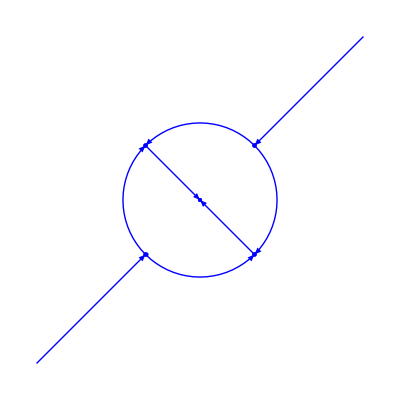

```mathematica
DomainPlot[GG[1.],Axes->False]
```

### Constructing the solution

R is the RHSolver, which we construct once for one choice of x (arbitrarily, x = 3).  U is then the solution.

```mathematica
R=RHSolver[GG[3.]];
U//Clear;U[x_]:=U[x]=R[GG[x]];
```

To evaluate the derivative of U (with respect to x), we need the minus values of Φ = I + C U

```mathematica
Cm=CauchyOperator[-1,R];
Φm//Clear;Φm[x_]:=Cm[U[x]]//AddIdentityMatrix;
Ux//Clear;Ux[x_]:=Ux[x]=R[GG[x],Φm[x]~FunListDot~GGx[x]];
```

We can now convert from U to the value and derivative of a variable y

```mathematica
y//Clear;
y[x_]:=y[x]=-x/(2 π)DomainIntegrate[#⟦1,2⟧&/@U[x]];
yx//Clear;
yx[x_]:=yx[x]=-1/(2 π)DomainIntegrate[#⟦1,2⟧&/@U[x]]-x/(2 π)DomainIntegrate[#⟦1,2⟧&/@Ux[x]]
```

u is the solution to Painlevé III

```mathematica
u//Clear;
u[x_]:=2 y[x] x/(x yx[x]-Θ∞ y[x] )
```

### Plotting the solution

We construct evaluate it at several Chebyshev points x to construct an approximation.  The numerical approximation is badly conditioned near 5.

```mathematica
Block[{x},Monitor[
uf=Fun[(x=#;u[#])&,Line[{3.,5.}],2^6+1]
,x];]
```

Here is a plot of the solution

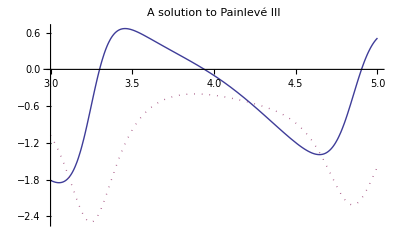

```mathematica
ReImPlot[uf[x]//Evaluate,{x,3.,5.},PlotStyle->{Thick,{Thick,Dotted}},PlotLabel->"A solution to Painlevé III"]
```

And here is the relative residual of the differential equation, demonstrating that we are indeed solving the Painlevé III ODE.

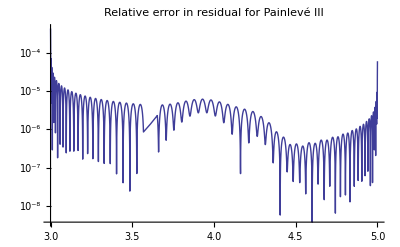

```mathematica
xf=Fun[#&,uf//Domain,uf//Length];
LogPlot[
(((uf'')-((uf')^2/uf -uf'/xf +4/xf (Θ0 uf^2+1-Θ∞)+4 uf^3-4/uf))/uf'')[x]//Abs//Evaluate,{x,3.,5.},
PlotRange->All,PlotStyle->Thick,PlotLabel->"Relative error in residual for Painlevé III"]
```

## Painleve IV

The Painlevé IV differential equation is

	u'' = (u')^2/(2 u) + 3/2 u^3+ 4 x u^2+(2+2 x^2-4 Θ_∞)u-(8 Θ^2)/u

This example is also based on an example in [Olver 2010] constructed from the RH problem in [Fokas et al. 2006].

### Setting up the jump curves

We choose an arbitrary choice of Stokes' multipliers, and the constants Θ_∞ and Θ.

```mathematica
Θ∞=1.123;
Θ=3.43;
Clear[s];{s[1],s[2],s[3],s[4]}=Array[s,4]/.(Solve[{s[1]==1,s[2]==2,s[3]==1/3,(1+s[2] s[3]) Exp[2 I π Θ∞]+(s[1] s[4]+(1+s[3] s[4])(1+s[1] s[2])) Exp[-2 I π Θ∞]==2 Cos[2 π Θ]},Array[s,4]])//First;

{S[1],S[2],S[3],S[4]}={({{1, 0}, {s[1], 1}}),({{1, s[2]}, {0, 1}}),({{1, 0}, {s[3], 1}}),({{1, s[4]}, {0, 1}})};
σ3=({{1, 0}, {0, -1}});
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

In this case EE is the matrix of eigenvectors.  However, we know the eigenvalues, and must ensure that the eigenvectors are in the correct order.

```mathematica
ord=((Dot@@Array[S,4]).MatrixExp[2I π Θ∞ σ3]//Eigenvalues)~NEqual~Diagonal[N[MatrixExp[-2I π Θ σ3]]];
EE=((Dot@@Array[S,4]).MatrixExp[2I π Θ∞ σ3]//Eigenvectors//(If[ord,#,Reverse[#]]&)//Transpose//Inverse)//N;
```

We can now construct the jump curves.

```mathematica
θ[x_,z_]:=(z^2/2+x z) ;
θx[x_,z_]:=(z) ;
Eθ[x_,z_]:={{ⅇ^(x z+z^2/2),0},{0,ⅇ^(-x z-z^2/2)}};
Eθx[x_,z_]:={{z ⅇ^(x z+z^2/2),0},{0,-z ⅇ^(-x z-z^2/2)}};
Emθ[x_,z_]:={{ⅇ^(-x z-z^2/2),0},{0,ⅇ^(x z+z^2/2)}};
Emθx[x_,z_]:={{-z ⅇ^(-x z-z^2/2),0},{0,z ⅇ^(x z+z^2/2)}};


G//Clear;
G[_,_][_,_?InfinityQ]:=IdentityMatrix[2];

G[-I,1][x_,z_]=Eθ[x,z].Inverse[({{z^Θ, 0}, {0, z^-Θ}}).EE.({{z^(Θ∞), 0}, {0, z^(-Θ∞)}})].Emθ[x,z]//Simplify;

G[I,1][x_,z_]=Eθ[x,z].({{z^Θ, 0}, {0, z^-Θ}}).EE.S[1].({{z^(Θ∞), 0}, {0, z^(-Θ∞)}}).Emθ[x,z]//FullSimplify;


G[I,-1][x_,z_]=Eθ[x,z].Inverse[({{PowerBranch[z,Θ,0], 0}, {0, PowerBranch[z,-Θ,0]}}).EE.S[1].S[2].({{PowerBranch[z,Θ∞,0], 0}, {0, PowerBranch[z,-Θ∞,0]}})].Emθ[x,z]//FullSimplify;

G[-I,-1][x_,z_]=Eθ[x,z].({{PowerBranch[z,Θ,0], 0}, {0, PowerBranch[z,-Θ,0]}}).EE.S[1].S[2].S[3].({{PowerBranch[z,Θ∞,0], 0}, {0, PowerBranch[z,-Θ∞,0]}}).Emθ[x,z]//FullSimplify;

G[-1,∞][x_,z_]=({{1, 0}, {s[3] Exp[-2 θ[x,z]] PowerBranch[z,2 Θ∞,0], 1}});
G[∞,-I][x_,z_]=({{1, -s[4] Exp[2 θ[x,z]] PowerBranch[z,-2 Θ∞,0]}, {0, 1}});
G[1,∞][x_,z_]=({{1, 0}, {s[1] Exp[-2 θ[x,z]] z^(2 Θ∞), 1}});
G[∞,I][x_,z_]=({{1, -s[2] Exp[2 θ[x,z]] z^(-2 Θ∞)}, {0, 1}});
```

With the jump functions defined, we construct a list of Funs.

```mathematica
GG//Clear;
GG[x_,tol_]:={
Fun[G[-I,1][x,#]&,Arc[0,1,{-π/2,0}],InterpolationPrecision->tol],
Fun[G[I,1][x,#]&,Arc[0,1,{π/2,0}],InterpolationPrecision->tol],
Fun[G[I,-1][x,#]&,Arc[0,1,{π/2,π}],InterpolationPrecision->tol],
Fun[G[-I,-1][x,#]&,Arc[0,1,{-π/2,-π}],InterpolationPrecision->tol],
Fun[G[1,∞][x,#]&,Line[{1,∞}],InterpolationPrecision->tol],
Fun[G[∞,I][x,#]&,Line[{∞ Exp[I π/2],I}],InterpolationPrecision->tol],
Fun[G[-1,∞][x,#]&,Line[{-1,-∞}],InterpolationPrecision->tol],
Fun[G[∞,-I][x,#]&,Line[{∞ Exp[-I π/2],-I}],InterpolationPrecision->tol]
}
```

The jump curve is defined over the domain:

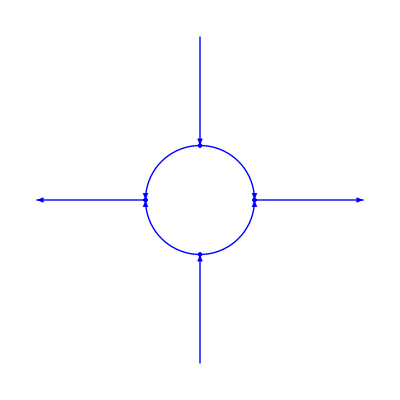

```mathematica
DomainPlot[GG[0.,10.^(-3)],Axes->False]
```

Again, we want to fix the length of to reuse computation.   We are going to compute the solution over the unit square

```mathematica
With[{tol=10.^(-4)},
lngs=Max/@({Length/@GG[-1.-1. I,tol],Length/@GG[1.+1.I,tol]}//Thread)
];
GG[x_]:={
Fun[G[-I,1][x,#]&,Arc[0,1,{-π/2,0}],lngs⟦1⟧],
Fun[G[I,1][x,#]&,Arc[0,1,{π/2,0}],lngs⟦2⟧],
Fun[G[I,-1][x,#]&,Arc[0,1,{π/2,π}],lngs⟦3⟧],
Fun[G[-I,-1][x,#]&,Arc[0,1,{-π/2,-π}],lngs⟦4⟧],
Fun[G[1,∞][x,#]&,Line[{1,∞}],lngs⟦5⟧],
Fun[G[∞,I][x,#]&,Line[{∞ Exp[I π/2],I}],lngs⟦6⟧],
Fun[G[-1,∞][x,#]&,Line[{-1,-∞}],lngs⟦7⟧],
Fun[G[∞,-I][x,#]&,Line[{∞ Exp[-I π/2],-I}],lngs⟦8⟧]
};
```

We also need the derivative:

```mathematica
Clear[Gx];
Gx[_,_][_,_?InfinityQ]:=ZeroMatrix[2]; 
Gx[-I,1][x_,z_]=D[G[-I,1][x,z],x]//Simplify;
Gx[I,1][x_,z_]=D[G[I,1][x,z],x]//Simplify;
Gx[I,-1][x_,z_]=D[G[I,-1][x,z],x]//Simplify;
Gx[-I,-1][x_,z_]=D[G[-I,-1][x,z],x]//Simplify;
Gx[1,∞][x_,z_]=D[G[1,∞][x,z],x]//Simplify;
Gx[∞,I][x_,z_]=D[G[∞,I][x,z],x]//Simplify;
Gx[-1,∞][x_,z_]=D[G[-1,∞][x,z],x]//Simplify;
Gx[∞,-I][x_,z_]=D[G[∞,-I][x,z],x]//Simplify;


GGx[x_]:={
Fun[Gx[-I,1][x,#]&,Arc[0,1,{-π/2,0}],lngs⟦1⟧],
Fun[Gx[I,1][x,#]&,Arc[0,1,{π/2,0}],lngs⟦2⟧],
Fun[Gx[I,-1][x,#]&,Arc[0,1,{π/2,π}],lngs⟦3⟧],
Fun[Gx[-I,-1][x,#]&,Arc[0,1,{-π/2,-π}],lngs⟦4⟧],
Fun[Gx[1,∞][x,#]&,Line[{1,∞}],lngs⟦5⟧],
Fun[Gx[∞,I][x,#]&,Line[{∞ Exp[I π/2],I}],lngs⟦6⟧],
Fun[Gx[-1,∞][x,#]&,Line[{-1,-∞}],lngs⟦7⟧],
Fun[Gx[∞,-I][x,#]&,Line[{∞ Exp[-I π/2],-I}],lngs⟦8⟧]
};
```

### Computing the solution

We now setup the RH solver again.

```mathematica
R//Clear;
R=RHSolver[GG[0.]];
U//Clear;
U[x_]:=U[x]=R[GG[x]];
```

Now we find the minus limits of the solution to the RH problem:

```mathematica
Cm=CauchyOperator[-1,R];
Φm//Clear;Φm[x_]:=Cm[U[x]]//AddIdentityMatrix;
Ux//Clear;Ux[x_]:=Ux[x]=R[GG[x],Φm[x]~FunListDot~GGx[x]];
```

We have functions y and u, where u solves Painlevé IV.  We determine y by the formula y = -2 lim_(z→∞)  z Cauchy[U,z]⟦1,2⟧ and y_x = -2 lim_(z→∞)  z Cauchy[Ux,z]⟦1,2⟧.

```mathematica
Clear[y,yx,u];
y[x_]:=y[x]=1/(π ⅈ)DomainIntegrate[U[x]]⟦1,2⟧;
yx[x_]:=yx[x]=1/(π ⅈ)DomainIntegrate[Ux[x]]⟦1,2⟧;
u[x_]:=-2x-yx[x]/y[x];
```

### The solution in the complex plane

Here's a plot of the real part of the computed solution in the complex plane

```mathematica
With[{sp=2^(-4)},
Monitor[
ListPlot3D[
Flatten[
Table[{x,t,u[x+I t]//Re},{x,-1,1,sp},{t,-1,1,sp}]
,1],
PlotLabel->"Real part of a solution to Painlevé IV in the complex plane"]
,{x,t}]
]
```

-Graphics3D-

## Ablowitz–Segur: Large positive x

In this example we use the simplest example of nonlinear steepest descent for homogenous Painlevé II with s_2 = 0 and s_1=-s_3=ⅈ s.  The deformation is based on [Fokas et al. 2006].  We first scale the RH problem by √(x/2), resulting in the new θ function and G function:

```mathematica
θ[z_]:=I(4/3 z^3 + z);
G//Clear;
s//Clear;
G[_][_,_,_?InfinityQ]:=IdentityMatrix[2];
G[1][s_,x_,z_]=({{Exp[-x^(3/2)  θ[z]], 0}, {0, Exp[x^(3/2)  θ[z]]}}).({{1, 0}, {I s, 1}}).({{Exp[x^(3/2)  θ[z]], 0}, {0, Exp[-x^(3/2)  θ[z]]}});
G[6][s_,x_,z_]=({{Exp[-x^(3/2)  θ[z]], 0}, {0, Exp[x^(3/2)  θ[z]]}}).({{1, I s}, {0, 1}}).({{Exp[x^(3/2)  θ[z]], 0}, {0, Exp[-x^(3/2)  θ[z]]}});
```

When x is positive, this has two stationary points at ±ⅈ/2. We need to know the paths of steepest descent eminating from this point and a sequence of points going to infinity.  Rather than trying to determine this analytically, we compute it numerically.  For x > 0, at the stationary point ⅈ/2, we know there are two paths of descent, one path T[x,r] corresponding to G[1] and approaching  ⅇ^(ⅈ π/6)∞ and one path Tm[x,r] corresponding to G[3] and approaching ⅇ^(5 ⅈ π/6)∞.  We thus interpolate in arcs centred at ⅈ/2of radius r in the complex plane to isolate each path.  Note that when x is complex, the path of steepest descent changes depending on arg x.

```mathematica
T//Clear;
T[_,_?NZeroQ]:=.5 I;
T[x_,r_]:=Fun[(Im[(x)^(3/2) θ[#]]-Im[(x)^(3/2) θ[I/2]])&,Arc[.5 I,r,{0.-Arg[x],π/2-0.1-Arg[x]}]]//Roots//First;
T[x_,_?InfinityQ]:=Exp[I (π/6-Arg[x]  /2)]∞;

Tm//Clear;
Tm[_,_?NZeroQ]:=.5 I;
Tm[x_,r_]:=Fun[(Im[(x)^(3/2) θ[#]]-Im[(x)^(3/2) θ[I/2]])&,Arc[.5 I,r,{3 π/4-Arg[x],π+π/4-Arg[x]}]]//Roots//First;
Tm[x_,_?InfinityQ]:=Exp[I (5 π/6-Arg[x]  /2)]∞;
```

We now determine points along the path of steepest descent, which approach the stationary point at a rate so that G is resolved with the same number of points.

```mathematica
ptsp[x_]:=T[x,#]&/@Join[1/Abs[x]^(3/4) Range[.5,3.,.5],{∞ }];
ptsm[x_]:=Tm[x,#]&/@Reverse[Join[1/Abs[x]^(3/4) Range[.5,3.,.5],{∞ }]];
pts[x_]:=Join[ptsm[x],{T[x,0.]},ptsp[x]];
```

Here is a plot of the computed points

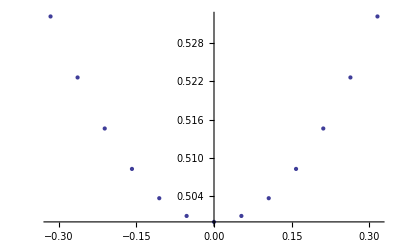

```mathematica
pts[20.]//ComplexDotPlot
```

The jump curve G[1]  is precisely the inverse of G[3].  Thus when we deform both curves to ±ⅈ/2, they cancel and become disjoint from G[4] and G[6].  We thus obtain the following jump curve (the parameter Stretch is the stretch of the rays going to infinity).  Since the InterpolationPrecision parameter is absolute accuracy (otherwise an unnecessary number of interpolation points would be used along curves where the jump curve is small), we have to trick the system to obtain relative accuracy, but only relative to the stationary point

```mathematica
GG//Clear;GG[s_,x_]:=GG[s,x]=ⅇ^(-(2 x^(3/2))/3)Join[
Fun[ⅇ^((2 x^(3/2))/3) (G[1][s,x,#]-IdentityMatrix[2]/.Underflow[]->0)&,Line[pts[x],Stretch->1/Abs[x]],InterpolationPrecision->10.^(-8)],
Fun[ⅇ^((2 x^(3/2))/3)(G[6][s,x,#]-IdentityMatrix[2]/.Underflow[]->0)&,Line[(-pts[x])//Reverse,Stretch->1/Abs[x]],InterpolationPrecision->10.^(-8)]
]//AddIdentityMatrix
```

Here is a plot of the new jump curve:

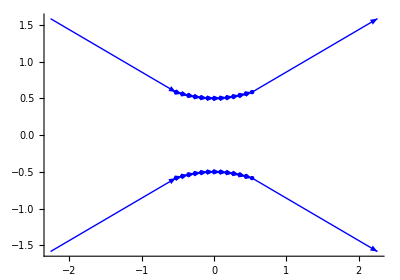

```mathematica
GG[1.,10.]//DomainPlot
```

For x near each other (say, inside blocks of size 3), we want to reuse the computation.  Thus we want the RH curves to be the same, and the length along each curve to be the same.   GG2 accomplishes this.

```mathematica
nr[x_]:=Floor[(x)/3]3+1.;
nrt[x_]:=nr[Abs[x]] Exp[I Arg[x]];

GG2//Clear;
GG2[s_,x_]:=Join[
Fun[(G[1][s,x,#]/.Underflow[]->0)&,Line[pts[nrt[x]],Stretch->1/Abs[nrt[x]]],Partition[Length/@GG[1,nrt[x]],Length[pts[nrt[x]]]-1]⟦1⟧],
Fun[(G[6][s,x,#]/.Underflow[]->0)&,Line[(-pts[nrt[x]])//Reverse,Stretch->1/Abs[nrt[x]]],Partition[Length/@GG[1,nrt[x]],Length[pts[nrt[x]]]-1]⟦2⟧]
]
```

We can now compute U.  We also need to scale the computed solution p.

```mathematica
R//Clear;
R[x_]:=R[x]=RHSolverTop[GG[1.,x]];
R2[x_]:=R[nr[x]];
U//Clear;U[s_,x_]:=GG2[s,x]//R2[x];
p//Clear;p[s_,x_]:=p[s,x]=-2 DomainIntegrate[U[s,x]]⟦2⟧/(2 π I) x^(1/2);
```

We can evaluate at large x

```mathematica
p[1.,10.]
```

-1.10475×10^-10-1.87016×10^-26 ⅈ

```mathematica
PainleveII[1.{I,0,-I},10.]
```

-1.10475×10^-10+4.61523×10^-29 ⅈ

```mathematica
p[2.,10.]
```

-2.20951×10^-10-3.74032×10^-26 ⅈ

```mathematica
PainleveII[2.{I,0,-I},10.]
```

-2.20951×10^-10+9.23047×10^-29 ⅈ

We can find the relative error of the approximation for the Hastings–McLeod solution (note that x = 10 the relative error between the Hastings–McLeod solution and the Airy function is already on the order of machine precision).  Note the jump in accuracy as we move from one block to the next, and that the method remains accurate in the asymptotic regime.

```mathematica
data=Partition[ReadList["RiemannHilbert/Data/McLeodSolution.txt",Number],7];
```

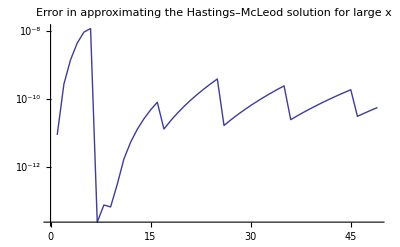

```mathematica
Monitor[Block[{x},
ListLineLogPlot[
((p[1.,x=First[#]]-#⟦3⟧)/#⟦3⟧//Abs)&/@data⟦660;;900;;5⟧
,PlotLabel->"Error in approximating the Hastings–McLeod solution for large x"]
],x]
```

We can also use this approach to compute other Ablowitz–Segur solutions.  Letting s become large and a pole appears.

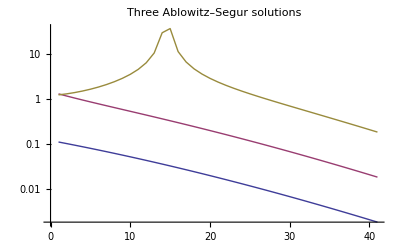

```mathematica
Monitor[Block[{x},
ListLineLogPlot[
{
(p[1.,x=First[#]])&/@data⟦660;;700⟧//Abs,
(p[10.,x=First[#]])&/@data⟦660;;700⟧//Abs,
(p[100.,x=First[#]])&/@data⟦660;;700⟧//Abs
},
PlotLabel->"Three Ablowitz–Segur solutions"]
],x]
```

## Sine Kernel

This is an example of an RH problem defined with loose ends, from [Deift, Its and Zhou 1997].  In general, loose ends cause singularities in the solutions.  However, because of the special form, the solution is actually still smooth on the domain, and hence (in a case of serendipity), the same numerical method can solve the RH problem

```mathematica
G[x_,z_]:=({{0, Exp[2 I z x]}, {-Exp[-2 I z x], 2}});
```

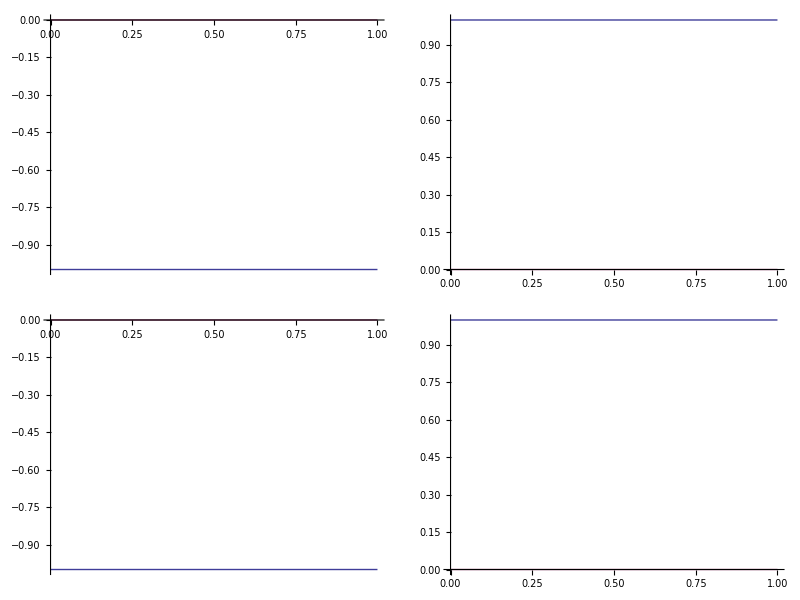
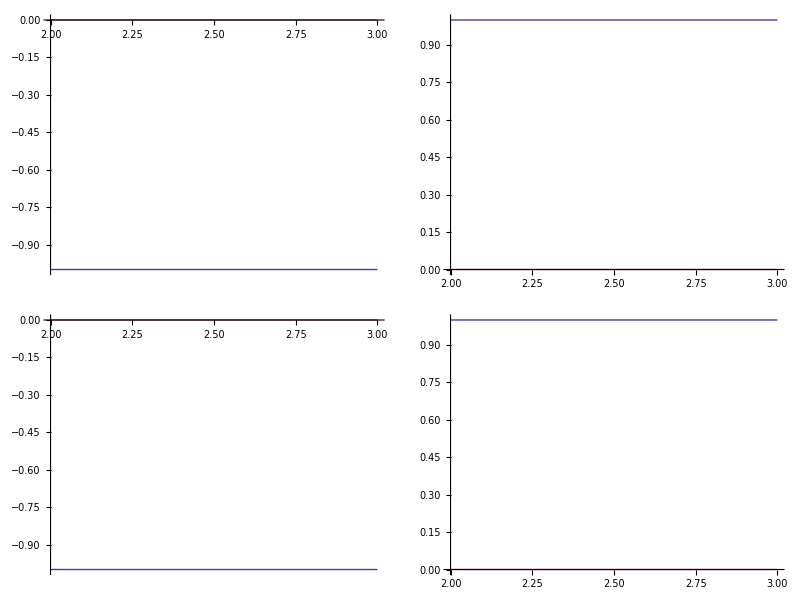
{(-Graphics-),(-Graphics-)}

```mathematica
U=Fun[G[x=0.,#]&,{Line[{0,1}],Line[{2,3}]},{20,20}]//RHSolve
```

We can confirm the accuracy of the jumps

```mathematica
(IdentityMatrix[2]+Cauchy[+1,U,.5])-(IdentityMatrix[2]+Cauchy[-1,U,.5]).G[x,.5]
```

{{8.32667×10^-16+3.747×10^-16 ⅈ,0.-6.245×10^-16 ⅈ},{9.4369×10^-16+3.747×10^-16 ⅈ,0.-6.245×10^-16 ⅈ}}

```mathematica
(IdentityMatrix[2]+Cauchy[+1,U,2.5])-(IdentityMatrix[2]+Cauchy[-1,U,2.5]).G[x,2.5]
```

{{5.55112×10^-17+6.38378×10^-16 ⅈ,-4.44089×10^-16+2.498×10^-16 ⅈ},{1.11022×10^-16+6.38378×10^-16 ⅈ,-6.66134×10^-16+2.498×10^-16 ⅈ}}

We repeat the exercise with larger x

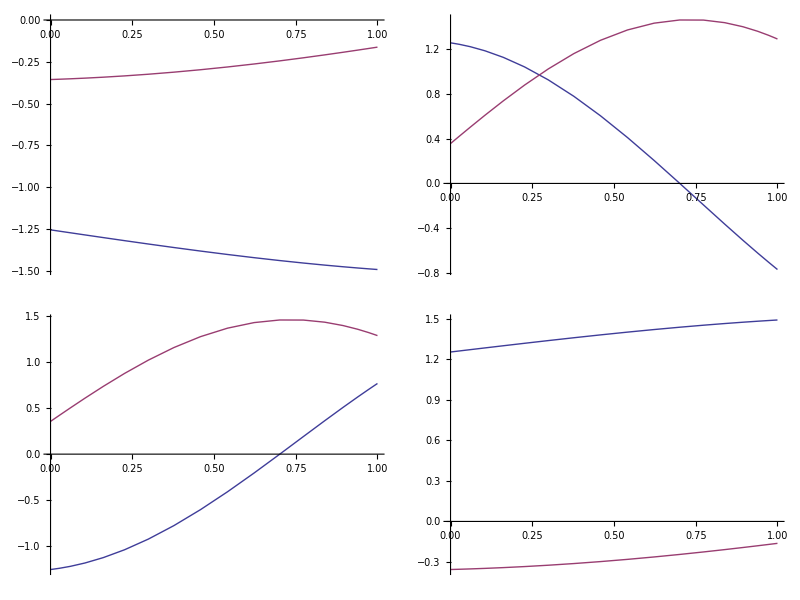
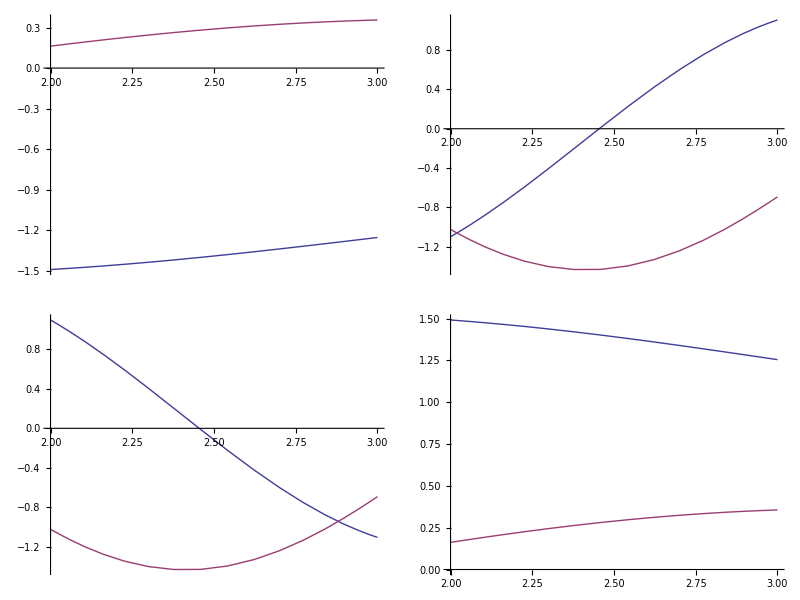
{(-Graphics-),(-Graphics-)}

```mathematica
U=Fun[G[x=1.,#]&,{Line[{0,1}],Line[{2,3}]},{20,20}]//RHSolve
```

We can confirm the accuracy of the jumps

```mathematica
(IdentityMatrix[2]+Cauchy[+1,U,.5])-(IdentityMatrix[2]+Cauchy[-1,U,.5]).G[x,.5]//Norm
```

2.72693×10^-15

```mathematica
(IdentityMatrix[2]+Cauchy[+1,U,2.5])-(IdentityMatrix[2]+Cauchy[-1,U,2.5]).G[x,2.5]//Norm
```

2.02639×10^-15

As x becomes larger, the solution becomes more oscillatory, and more collocation points are needed

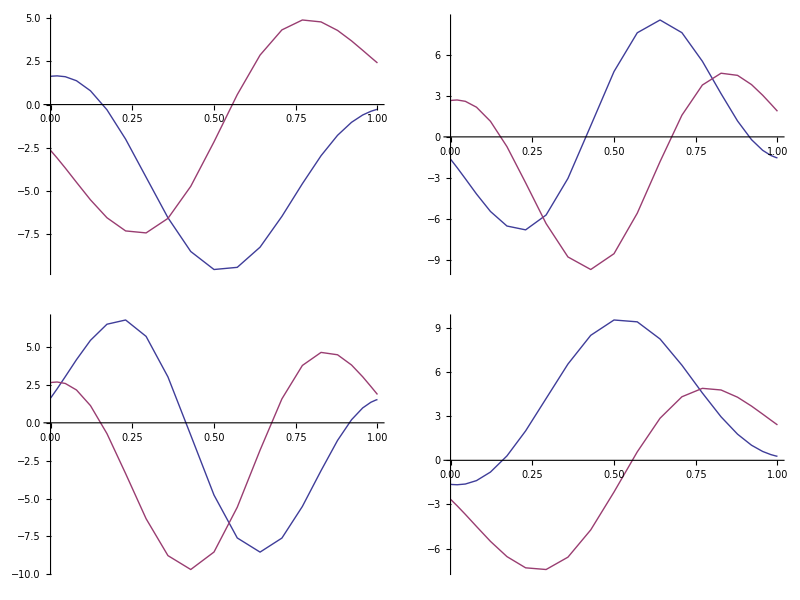
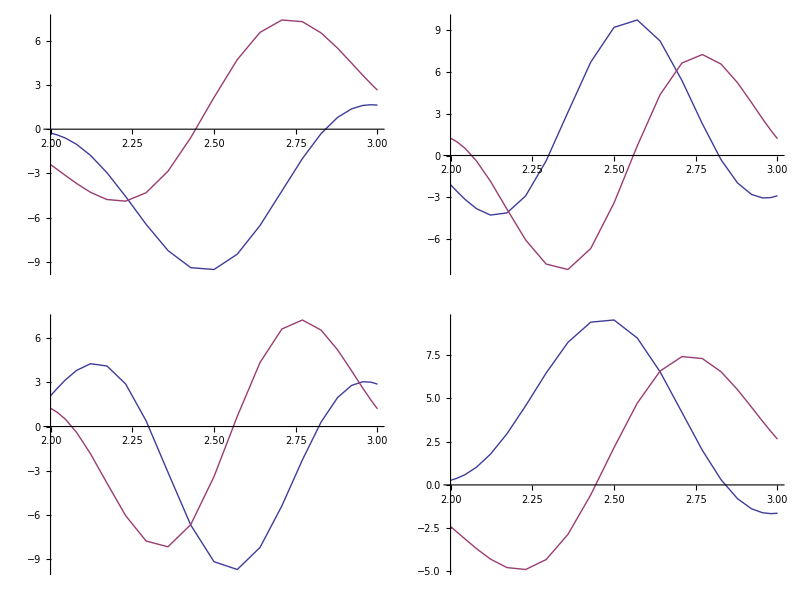
{(-Graphics-),(-Graphics-)}

```mathematica
U=Fun[G[x=5.,#]&,{Line[{0,1}],Line[{2,3}]}]//RHSolve
```

```mathematica
Length/@U
```

{23,23}

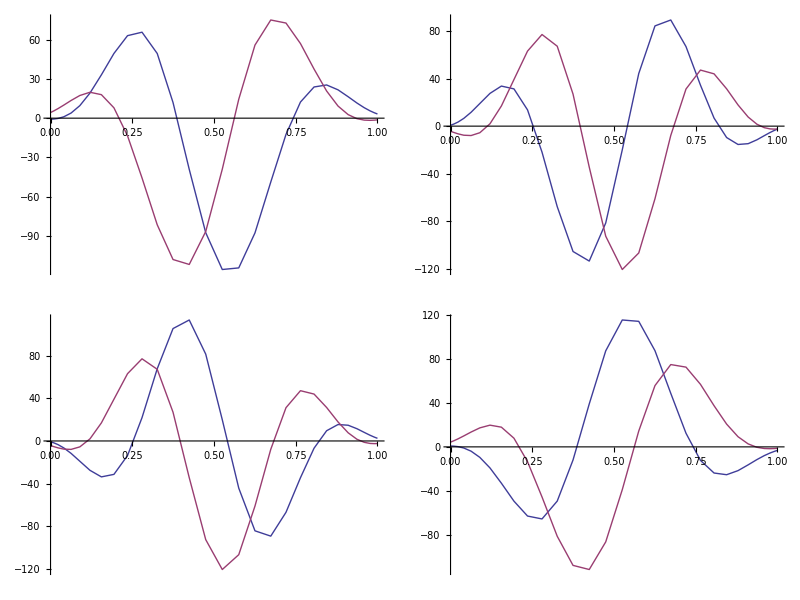
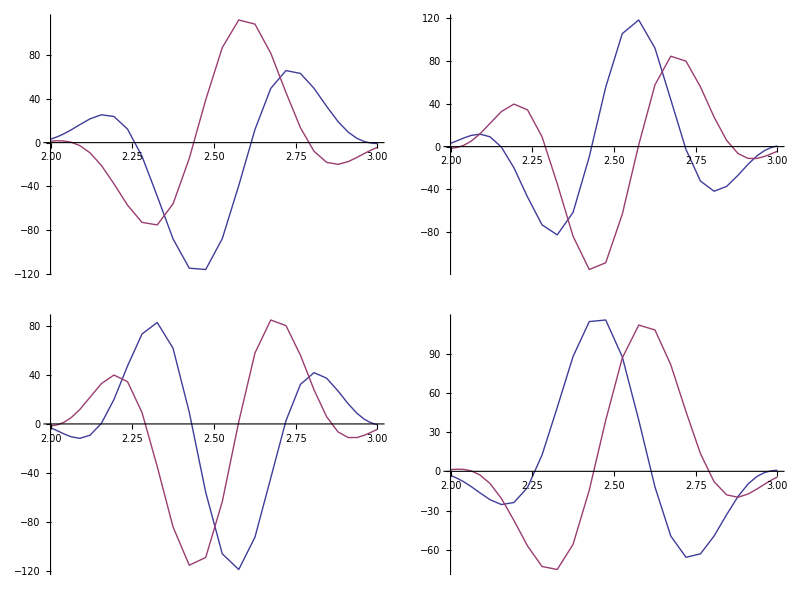
{(-Graphics-),(-Graphics-)}

```mathematica
U=Fun[G[x=10.,#]&,{Line[{0,1}],Line[{2,3}]}]//RHSolve
```

```mathematica
Length/@U
```

{32,32}

The system is also becoming less well-conditioned, causing errors

```mathematica
U=Fun[G[x=10.,#]&,{Line[{0,1}],Line[{2,3}]}]//RHSolve;(IdentityMatrix[2]+Cauchy[+1,U,.5])-(IdentityMatrix[2]+Cauchy[-1,U,.5]).G[x,.5]//Norm
```

8.31386×10^-13

```mathematica
U=Fun[G[x=20.,#]&,{Line[{0,1}],Line[{2,3}]}]//RHSolve;(IdentityMatrix[2]+Cauchy[+1,U,.5])-(IdentityMatrix[2]+Cauchy[-1,U,.5]).G[x,.5]//Norm
```

2.06928×10^-11

```mathematica
U=Fun[G[x=50.,#]&,{Line[{0,1}],Line[{2,3}]}]//RHSolve;(IdentityMatrix[2]+Cauchy[+1,U,.5])-(IdentityMatrix[2]+Cauchy[-1,U,.5]).G[x,.5]//Norm
```

3.26293×10^-7

```mathematica
U=Fun[G[x=100.,#]&,{Line[{0,1}],Line[{2,3}]}]//RHSolve;(IdentityMatrix[2]+Cauchy[+1,U,.5])-(IdentityMatrix[2]+Cauchy[-1,U,.5]).G[x,.5]//Norm
```

2.6828×10^-6

The speed of the algorithm has also slowed down, as the number of collocation points has increased considerably:

```mathematica
Length/@U
```

{144,144}

Deformation of the RH problem would be needed to avoid this growth in error and computational cost

## References

A. S. Fokas, A. R. Its, A. A. Kapaev & V. Yu. Novokshenov (2006), Painlevé Transcendents: the Riemann–Hilbert approach, AMS. 

S. Olver (2010), A general framework for solving Riemann–Hilbert problems numerically, Report no. NA-10/5, Mathematical Institute, Oxford University.

S. Olver (2009b), Numerical solution of Riemann–Hilbert problems: Painlevé II, to appear in Found. Comput. Maths.

S. Olver (2009a), Computing the Hilbert transform and its inverse, to appear in Maths Comp.